## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["../_Data/supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeFunc[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
incidFunc[[All,selectPos]]
];
```

```mathematica
Clear[calcRank];
calcRank[net_,type_,alpha_]:=calcRank[net,type,alpha]=Module[{d,s,vv,sg,ng,temp,maxRank,centrality,comps},
comps=ConnectedComponents[net[[2]]];
sg=Subgraph[net[[2]],comps[[1]]];
centrality=ConstantArray[0,VertexCount@net[[2]]];

Switch[type,
"d",d=VertexDegree[sg];s=Total@WeightedAdjacencyMatrix[sg];centrality[[VertexList[sg]]]=Switch[alpha,0,d,1,s,_,(If[#==0,0,#^(1-alpha)]&/@d)s^alpha]; (* following: Opsahl et al. 2010*),
"e",{vv}=Eigenvectors[1.Normal@If[alpha==0,AdjacencyMatrix[sg],WeightedAdjacencyMatrix[sg]],1];
centrality[[VertexList[sg]]]=Normalize[Abs[vv],Total];,
"b",ng=Graph[VertexList[net[[2]]],{Null,AdjacencyMatrix[net[[2]]]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[net[[2]],EdgeWeight]^-alpha];centrality=BetweennessCentrality[ng];,
"c",ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-alpha];
centrality[[VertexList[sg]]]=ClosenessCentrality[ng];
];

temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1]
];
cent2rank[centrality_]:=Module[{temp,maxRank},
temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1];
temp[[All,2]]
];
```

```mathematica
(* https://mathematica.stackexchange.com/questions/131818/why-does-weightedadjacencymatrix-take-the-weight-for-absent-edges-to-be-zero
https://mathematica.stackexchange.com/questions/131834/directly-change-the-background-value-of-a-sparsearray 
https://mathematica.stackexchange.com/questions/131834/directly-change-the-background-value-of-a-sparsearray
https://mathematica.stackexchange.com/questions/164671/remove-or-change-edge-weights-of-graph-with-good-performance
*)
setBackground[Verbatim[SparseArray][a_,b_,_,c__],new_]:=SparseArray[a,b,new,{c[[1]],c[[2]],c[[3]]^1}];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
segments={1243,1248,1250,1252,1254,1257};
nets=Table[
makeNet[segments[[c]],segments[[c+1]]-1]
,{c,1,Length@segments-1}];
```

## Export networks for Gephi and plot

### Confusion matrix of noblemen participating in the analysed networks

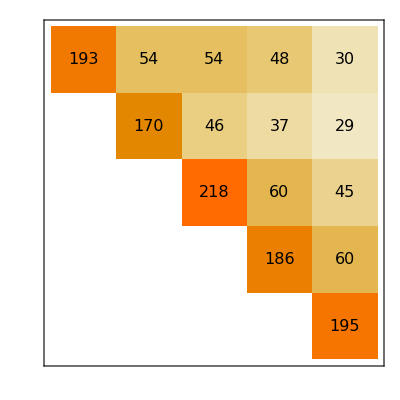

```mathematica
MatrixPlot[
Table[
If[i≤j,
Length@Intersection[
ConnectedComponents[nets[[i]][[2]]][[1]],ConnectedComponents[nets[[j]][[2]]][[1]]
],-1]
,{i,1,Length@nets},{j,1,Length@nets}]
,ColorFunction->Automatic,PlotRange->{0,320},ClippingStyle->White,FrameStyle->Directive[White],FrameTicks->{{None,Table[
{c,ToString@cezury[[c]]<>"-\n-"<>ToString[segments[[c+1]]-1]}
,{c,1,Length@segments-1}]},{None,Table[
{c,ToString@segments[[c]]<>"-\n-"<>ToString[segments[[c+1]]-1]}
,{c,1,Length@segments-1}]}},FrameTicksStyle->Directive[FontFamily->"Helvetica",Black,14],
Epilog->Flatten@Table[
Inset[Style[
ToString@Length@Intersection[
ConnectedComponents[nets[[i]][[2]]][[1]],ConnectedComponents[nets[[j]][[2]]][[1]]
],FontFamily->"Helvetica",Black,16
],{i,6-j}-0.5]
,{i,1,Length@nets},{j,1,i}]
]
```

### Check reach of the kings

```mathematica
tab=Table[
temp=nets[[i]];
sg=temp[[2]];
ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-1];
gd=GraphDistanceMatrix[ng];
nnO=Position[Thread[gd[[1979]]>gd[[1553]]],True]//Flatten;
nnV=Position[Thread[gd[[1979]]<gd[[1553]]],True]//Flatten;
{ToString@segments[[i]]<>"-"<>ToString[segments[[i+1]]-1],1.(Length@nnV-1)/(Length[ConnectedComponents[ng][[1]]]-1),1.(Length@nnO-1)/(Length[ConnectedComponents[ng][[1]]]-1)}
,{i,1,5}];
```

```mathematica
Grid@Prepend[tab,{"year"}~Join~names[[{1979,1553}]]]
```

year | Václav I. | Přemysl II.
1243-1247 | 0.744792 | 0.239583
1248-1249 | 0.508876 | 0.420118
1250-1251 | 0.156682 | 0.700461
1252-1253 | 0.0864865 | 0.902703
1254-1256 | 0. | 1.

### Define loyal/rebel nodes for colouring and naming

```mathematica
(* loyals from historiography *)
loyal=Flatten@{{ 238},{599,811,112},{518,1791,752,859,1056},{806,514},{1277,2302},{642,330,906,900,1832}};
names[[loyal]]
(* rebels from historiography *)
rebel={2070,1392,306,143,1350,381,757,1692,1817,2041,707,941,1183,1850,145,327,376};
names[[rebel]]
```

{Boreš, syn Bohuslava z Rýzmberka,Havel z Lemberka,Jaroslav z Hruštice, syn Markvarta,Beneš, syn Heřmana, bratr Markvarta,Erkembreht de Starkenberk,Siffrido de Colbowe,Jan Losos,Jindřich Král,Lutholdus,Jaroš ze Slivna,Eppo ze Slivna, bratr Jaroše,Ojíř z Frídberka,Zdeslav ze Šternberka, syn Diviše,Hirzo,Častolov, syn Smila, bratr Jindřicha,Jindřich, syn Smila, bratr Častolova,Jindřich, syn Častolova,Smil z Lichtenburka}

{Vítek z Hradce, syn Jindřicha,Pardus,Budivoj, bra Parduse a Sudomíra,Blud, bratr Oneše,Oneš, syn Bicena z Pňovic,Ctibor z Lipnice,Jan z Deblína, syn Ratibora,Ratibor z Deblína,Slavibor z Drnovic,Vilém z Náměšti, syn Slavibora,Idík, syn Milíče,Kojata, b Viléma z Náměšti,Milíč z Náměšti,Spitata z Moravičan,Boček z Jaroslavic,Častolov z Čeblovic, bratr Crha,Crh, bratr Častolova}

```mathematica
(* 10 highest ranking individuals - kings excluded *)
chosen10=Table[
MaximalBy[Delete[calcRank[nets[[i]],"c",1.5],{{1979},{1553}}],Last,10][[All,1]]
,{i,1,5}];
names[[#]]&/@chosen10
```

{{Crh, bratr Častolova,Vítek z Hradce, syn Jindřicha,Milíč z Náměšti,Častolov z Čeblovic, bratr Crha,Ratibor z Deblína,Boček z Jaroslavic,Vítek mladší z Příběnic,Jan z Deblína, syn Ratibora,Havel z Lemberka,Sifridus sirotek},{Havel z Lemberka,Boreš, syn Bohuslava z Rýzmberka,Jaroš ze Slivna,Ojíř z Frídberka,Častolov, syn Smila, bratr Jindřicha,Jindřich, syn Častolova,Pavlík,Sifridus sirotek,Vilém z Hustopeč,Milíč z Náměšti},{Boček z Jaroslavic,Crh, bratr Častolova,Blud, syn Onše,Pardus,Smil ze Střílek,Bohuš z Čeblovic,Vítek z Hradce, syn Jindřicha,Beneda Bludone,Sláva,Milíč z Náměšti},{Zdeslav ze Šternberka, syn Diviše,Boček z Jaroslavic,Beneš ze Cvilína,Jaroš ze Slivna,Havel z Lemberka,Jan z Deblína, syn Ratibora,Vítek z Hradce, syn Jindřicha,Bohuš z Čeblovic,Kuno z Kunštátu,Milíč z Náměšti},{Smil ze Střílek,Beneš ze Cvilína,Kuno z Kunštátu,Markvart z Dunajovic,Jan z Deblína, syn Ratibora,Vítek z Hradce, syn Jindřicha,Pardus,Idík, syn Milíče,Sudomír z Žeravic,Bohuš z Čeblovic}}

### Export nodes and edges of largest connected components

```mathematica
Do[
temp=nets[[j]];
sg=temp[[2]];
cc=ConnectedComponents[sg][[1]];
ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-1];
gd=GraphDistanceMatrix[ng];
nnO=Position[Thread[gd[[1979]]>gd[[1553]]],True]//Flatten;
nnV=Position[Thread[gd[[1979]]<gd[[1553]]],True]//Flatten;

Export["../_Networks/net"<>ToString@segments[[j]]<>"-"<>ToString[segments[[j+1]]-1]<>"_nodes.csv",
Join[{"Id\tLabel\tcolor"}
,Table[
StringRiffle[
ToString/@{i,
If[MemberQ[chosen10[[j]],i]||MemberQ[{1979,1553},i],""<>StringReplace[names[[i]],{" z "->" of "," ze "->" of ","syn"->" s/o","bratr"->" b/o","Václav I."->"Wenceslas","Přemysl II."->"Přemysl Otakar"}]<>"",""],
Which[MemberQ[rebel,i],"#ff335e",MemberQ[loyal,i],"#00eb17",MemberQ[{1979,1553},i],"#b700c7",MemberQ[nnO,i],"#FFB7C5",MemberQ[nnV,i],"#CEFFA3",True,"#5cb6ff"]},"\t"]
,{i,cc}]]
,"Text"];

nodeList=Rule@@#&/@Transpose[{Range[Length@cc],cc}];
Export[
"../_Networks/net"<>ToString@segments[[j]]<>"-"<>ToString[segments[[j+1]]-1]<>"_edges.csv",
Join[{"Source\tTarget\tWeight"},
Join[#[[1]]/.nodeList,{#[[2]]}]&/@Drop[ArrayRules@AdjacencyMatrix[sg][[cc,cc]],-1]],"Table"
];

,{j,1,5}];
```

### Example network plot

```mathematica
temp=nets[[j]];
sg=temp[[2]];
cc=ConnectedComponents[sg][[1]];
ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-1];
gd=GraphDistanceMatrix[ng];
nnO=Position[Thread[gd[[1979]]>gd[[1553]]],True]//Flatten;
nnV=Position[Thread[gd[[1979]]<gd[[1553]]],True]//Flatten;
```

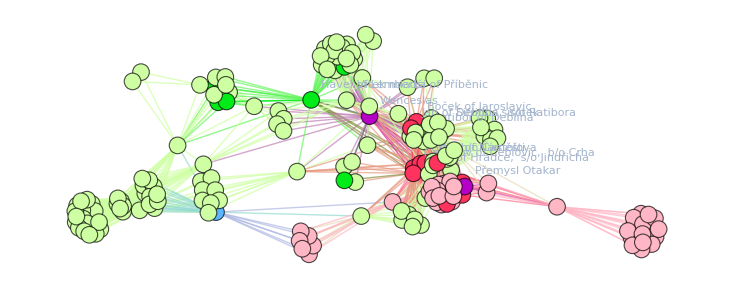

```mathematica
HighlightGraph[
Subgraph[sg,cc,EdgeShapeFunction->({Blend[{colorfunc[#2[[1]]],colorfunc[#2[[2]]]},0.5],Line[#1]}&),
VertexLabels->(#->StringReplace[names[[#]],{" z "->" of "," ze "->" of ","syn"->" s/o","bratr"->" b/o","Václav I."->"Wenceslas","Přemysl II."->"Přemysl Otakar"}]&/@Join[chosen10[[j]],{1979,1553}])],
Style[#,RGBColor[Which[MemberQ[rebel,#],"#ff335e",MemberQ[loyal,#],"#00eb17",MemberQ[{1979,1553},#],"#b700c7",MemberQ[nnO,#],"#FFB7C5",MemberQ[nnV,#],"#CEFFA3",True,"#5cb6ff"]],PointSize[0.01]]&/@cc,
VertexSize->5.,ImageSize->Large]
```